```mathematica
kNNcancerFile = FileNameJoin[{NotebookDirectory[],"../../src/results/kNN/test_convergence.cancer.precis.dat"}];
kNNglassFile = FileNameJoin[{NotebookDirectory[],"../../src/results/kNN/test_convergence.glass.precis.dat"}];
kNNirisFile = FileNameJoin[{NotebookDirectory[],"../../src/results/kNN/test_convergence.iris.precis.dat"}];
kNNsoybeanFile = FileNameJoin[{NotebookDirectory[],"../../src/results/kNN/test_convergence.soybean.precis.dat"}];
kNNvoteFile = FileNameJoin[{NotebookDirectory[],"../../src/results/kNN/test_convergence.vote.precis.dat"}];
```

```mathematica
NBcancerFile = FileNameJoin[{NotebookDirectory[],"../../src/results/NaiveBayes/test_convergence.cancer.precis.dat"}];
NBglassFile = FileNameJoin[{NotebookDirectory[],"../../src/results/NaiveBayes/test_convergence.glass.precis.dat"}];
NBirisFile = FileNameJoin[{NotebookDirectory[],"../../src/results/NaiveBayes/test_convergence.iris.precis.dat"}];
NBsoybeanFile = FileNameJoin[{NotebookDirectory[],"../../src/results/NaiveBayes/test_convergence.soybean.precis.dat"}];
NBvoteFile = FileNameJoin[{NotebookDirectory[],"../../src/results/NaiveBayes/test_convergence.vote.precis.dat"}];
```

```mathematica
TANcancerFile = FileNameJoin[{NotebookDirectory[],"../../src/results/TAN/test_convergence.cancer.precis.dat"}];
TANglassFile = FileNameJoin[{NotebookDirectory[],"../../src/results/TAN/test_convergence.glass.precis.dat"}];
TANirisFile = FileNameJoin[{NotebookDirectory[],"../../src/results/TAN/test_convergence.iris.precis.dat"}];
TANsoybeanFile = FileNameJoin[{NotebookDirectory[],"../../src/results/TAN/test_convergence.soybean.precis.dat"}];
TANvoteFile = FileNameJoin[{NotebookDirectory[],"../../src/results/TAN/test_convergence.vote.precis.dat"}];
```

```mathematica
ID3cancerFile = FileNameJoin[{NotebookDirectory[],"../../src/results/ID3/test_convergence.cancer.precis.dat"}];
ID3glassFile = FileNameJoin[{NotebookDirectory[],"../../src/results/ID3/test_convergence.glass.precis.dat"}];
ID3irisFile = FileNameJoin[{NotebookDirectory[],"../../src/results/ID3/test_convergence.iris.precis.dat"}];
ID3soybeanFile = FileNameJoin[{NotebookDirectory[],"../../src/results/ID3/test_convergence.soybean.precis.dat"}];
ID3voteFile = FileNameJoin[{NotebookDirectory[],"../../src/results/ID3/test_convergence.vote.precis.dat"}];
```

```mathematica
kNNcancerData=ReadList[kNNcancerFile,Number,RecordLists->True];
kNNglassData=ReadList[kNNglassFile,Number,RecordLists->True];
kNNirisData=ReadList[kNNirisFile,Number,RecordLists->True];
kNNsoybeanData=ReadList[kNNsoybeanFile,Number,RecordLists->True];
kNNvoteData=ReadList[kNNvoteFile,Number,RecordLists->True];
```

```mathematica
NBcancerData=ReadList[NBcancerFile,Number,RecordLists->True];
NBglassData=ReadList[NBglassFile,Number,RecordLists->True];
NBirisData=ReadList[NBirisFile,Number,RecordLists->True];
NBsoybeanData=ReadList[NBsoybeanFile,Number,RecordLists->True];
NBvoteData=ReadList[NBvoteFile,Number,RecordLists->True];
```

```mathematica
TANcancerData=ReadList[TANcancerFile,Number,RecordLists->True];
TANglassData=ReadList[TANglassFile,Number,RecordLists->True];
TANirisData=ReadList[TANirisFile,Number,RecordLists->True];
TANsoybeanData=ReadList[TANsoybeanFile,Number,RecordLists->True];
TANvoteData=ReadList[TANvoteFile,Number,RecordLists->True];
```

```mathematica
ID3cancerData=ReadList[ID3cancerFile,Number,RecordLists->True];
ID3glassData=ReadList[ID3glassFile,Number,RecordLists->True];
ID3irisData=ReadList[ID3irisFile,Number,RecordLists->True];
ID3soybeanData=ReadList[ID3soybeanFile,Number,RecordLists->True];
ID3voteData=ReadList[ID3voteFile,Number,RecordLists->True];
```

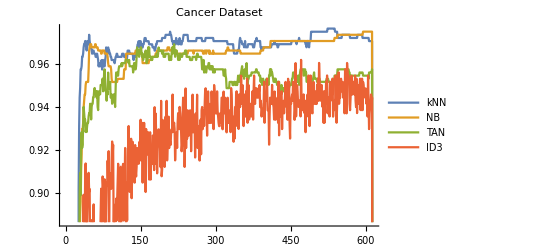

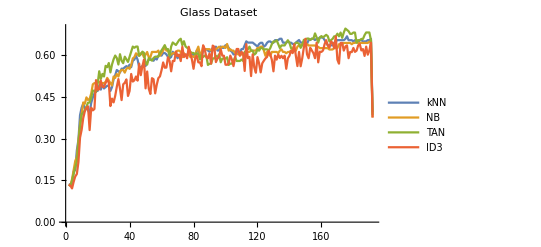

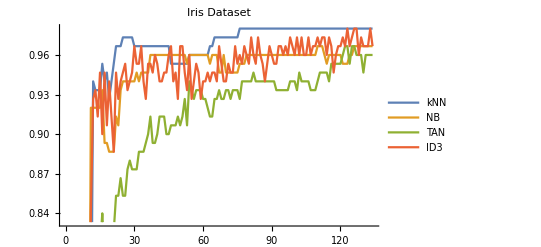

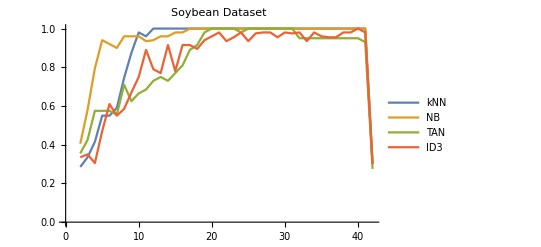

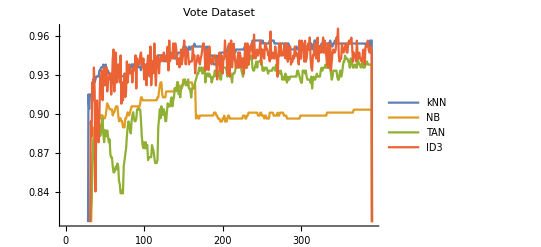

```mathematica
ListLinePlot[{kNNcancerData,NBcancerData,TANcancerData,ID3cancerData},FrameLabel->{"Size of Training Dataset","Average Precision"},PlotLabel->"Cancer Dataset",PlotLegends->{"kNN", "NB","TAN","ID3"}]
ListLinePlot[{kNNglassData,NBglassData,TANglassData,ID3glassData},FrameLabel->{"Size of Training Dataset","Average Precision"},PlotLabel->"Glass Dataset",PlotLegends->{"kNN", "NB","TAN","ID3"}]
ListLinePlot[{kNNirisData,NBirisData,TANirisData,ID3irisData},FrameLabel->{"Size of Training Dataset","Average Precision"},PlotLabel->"Iris Dataset",PlotLegends->{"kNN", "NB","TAN","ID3"}]
ListLinePlot[{kNNsoybeanData,NBsoybeanData,TANsoybeanData,ID3soybeanData},FrameLabel->{"Size of Training Dataset","Average Precision"},PlotLabel->"Soybean Dataset",PlotLegends->{"kNN", "NB","TAN","ID3"}]
ListLinePlot[{kNNvoteData,NBvoteData,TANvoteData,ID3voteData},FrameLabel->{"Size of Training Dataset","Average Precision"},PlotLabel->"Vote Dataset",PlotLegends->{"kNN", "NB","TAN","ID3"}]
```